Name: Karan Sharma 
College Roll No.: 2232191
University Roll No.: 22036563079 
Course: BSc. (Hons.) Mathematics/Year 3/Complex Analysis 
Section: A

## Practical 7 Plotting the horizontal & vertical lines and the corresponding grid. Also the image of the grid under a given function.

Question 1: Plot the lines y = a, where a = -1/2, -1, 1/2, 1; the lines x = a where a = -1/2, -1, 1/2, 1; and the corresponding grid. Also find the image of this grid under the mapping f(z) = 1/z .

```mathematica
f[z_] := 1 / z
```

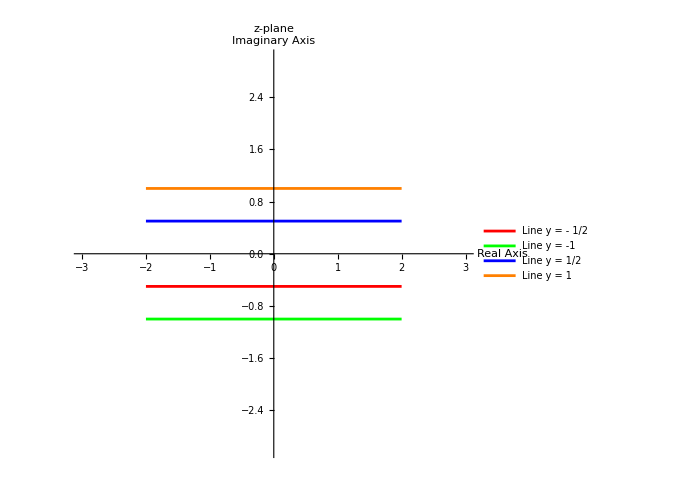

```mathematica
a1 = ParametricPlot[Evaluate[Table[{Re[t + ⅈ a], Im[t + ⅈ a]}, {a, {- 1/2 , -1, 1/2 , 1}}]], {t, -2, 2}, PlotStyle -> {Red, Green, Blue, Orange}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z-plane", PlotLegends -> {"Line y = - 1/2 ", "Line y = -1", "Line y = 1/2 ", "Line y = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

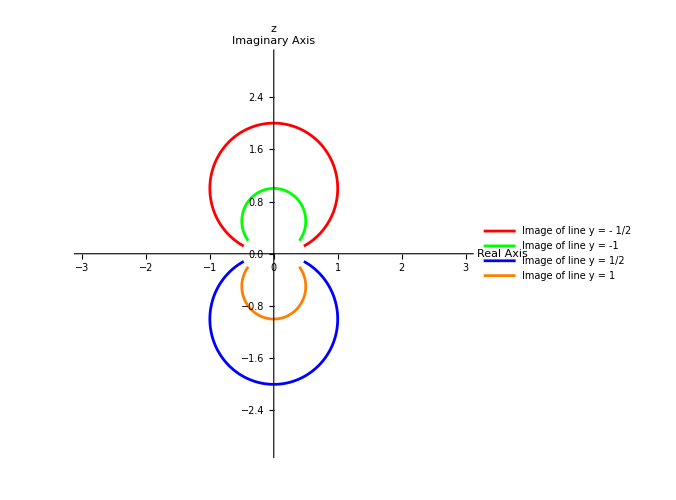

```mathematica
b1 = ParametricPlot[ Evaluate[Table[{Re[f[t + ⅈ a]], Im[f[t + ⅈ a]]}, {a, {- 1/2 , -1, 1/2 , 1}}]], {t, -2, 2}, PlotStyle -> {Red, Green, Blue, Orange}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Image of line y = - 1/2 ", "Image of line y = -1", "Image of line y = 1/2 ", "Image of line y = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

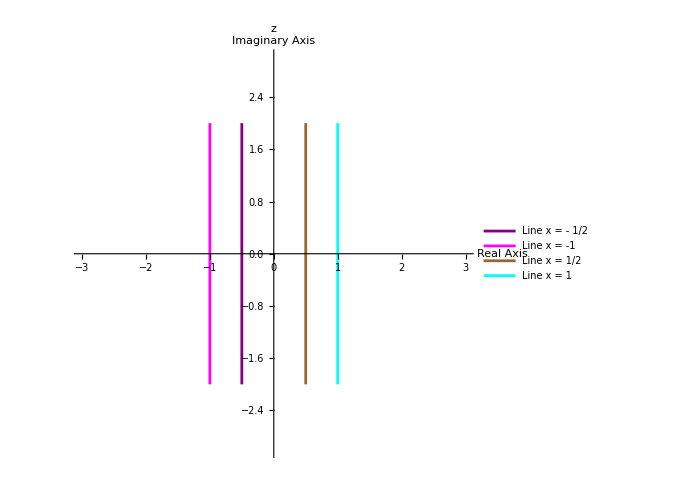

```mathematica
a2 = ParametricPlot[Evaluate[Table[{Re[a + ⅈ t], Im[a +ⅈ t]}, {a, {- 1/2 , -1, 1/2 , 1}}]], {t, -2, 2}, PlotStyle -> {Purple, Magenta, Brown, Cyan}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Line x = - 1/2 ", "Line x = -1", "Line x = 1/2 ", "Line x = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

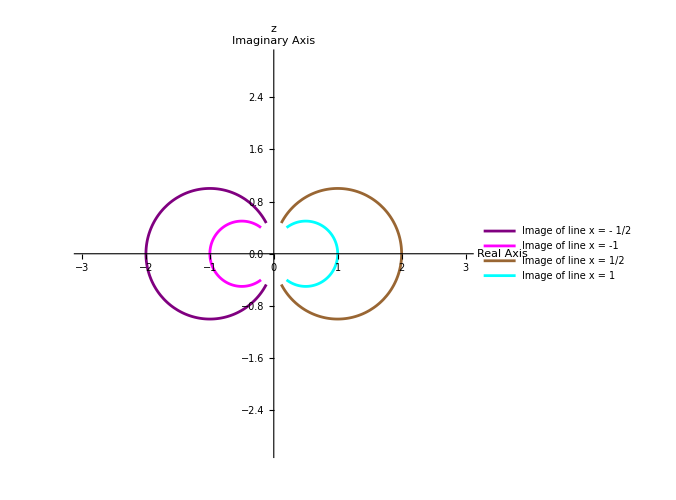

```mathematica
b2 = ParametricPlot[ Evaluate[Table[{Re[f[a + ⅈ t]], Im[f[a + ⅈ t]]}, {a, {- 1/2 , -1, 1/2 , 1}}]], {t, -2, 2}, PlotStyle -> {Purple, Magenta, Brown, Cyan}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Image of line x = - 1/2 ", "Image of line x = -1", "Image of line x = 1/2 ", "Image of line x = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

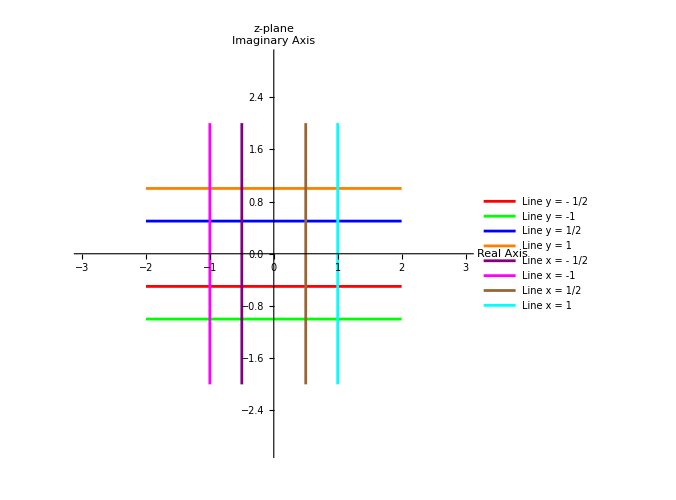
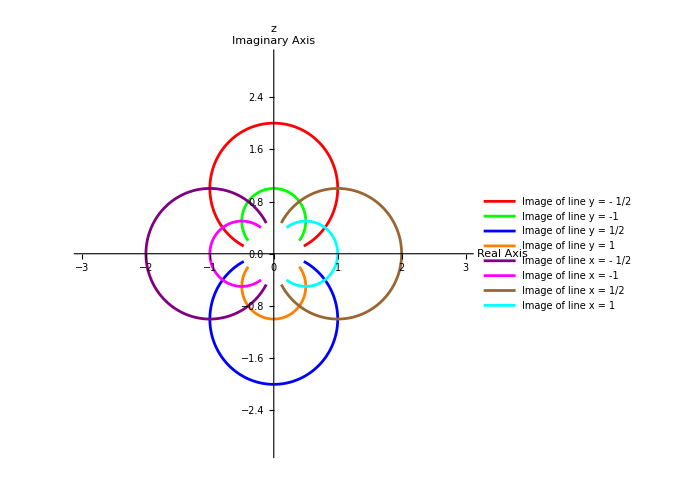

```mathematica
{Show[a1, a2], Show[b1, b2]}
```

Question 2: Plot the lines y = a, where a = 1/4 , 1/2 , 3/4 , 1; the lines x = a, where a = 1/4 , 1/2 , 3/4 , 1 and the corresponding grid. Also find the image of this grid under the mapping f(z) = z^2.

```mathematica
f[z_] := z^2
```

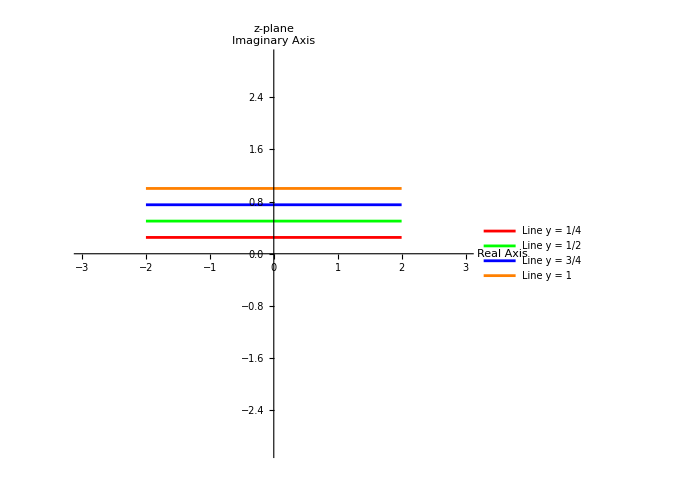

```mathematica
a1 = ParametricPlot[Evaluate[Table[{Re[t + ⅈ a], Im[t + ⅈ a]}, {a, {1/4, 1/2, 3/4, 1}}]], {t, -2, 2}, PlotStyle -> {Red, Green, Blue, Orange}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z-plane", PlotLegends -> {"Line y = 1/4 ", "Line y = 1/2", "Line y = 3/4 ", "Line y = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

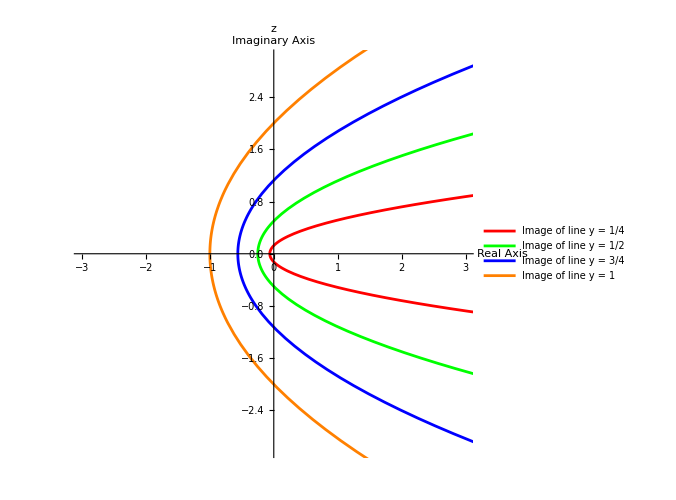

```mathematica
b1 = ParametricPlot[ Evaluate[Table[{Re[f[t + ⅈ a]], Im[f[t + ⅈ a]]}, {a, {1/4,1/2,3/4,1}}]], {t, -2, 2}, PlotStyle -> {Red, Green, Blue, Orange}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Image of line y = 1/4 ", "Image of line y = 1/2", "Image of line y = 3/4 ", "Image of line y = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

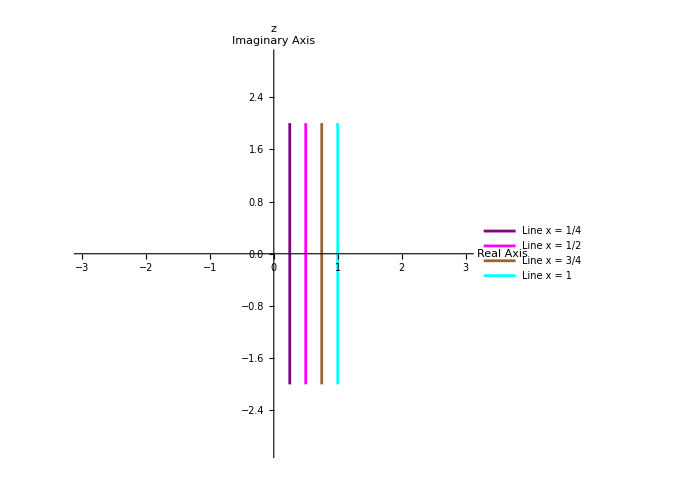

```mathematica
a2 = ParametricPlot[Evaluate[Table[{Re[a + ⅈ t], Im[a +ⅈ t]}, {a, {1/4,1/2,3/4,1}}]], {t, -2, 2}, PlotStyle -> {Purple, Magenta, Brown, Cyan}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Line x = 1/4 ", "Line x = 1/2", "Line x = 3/4 ", "Line x = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

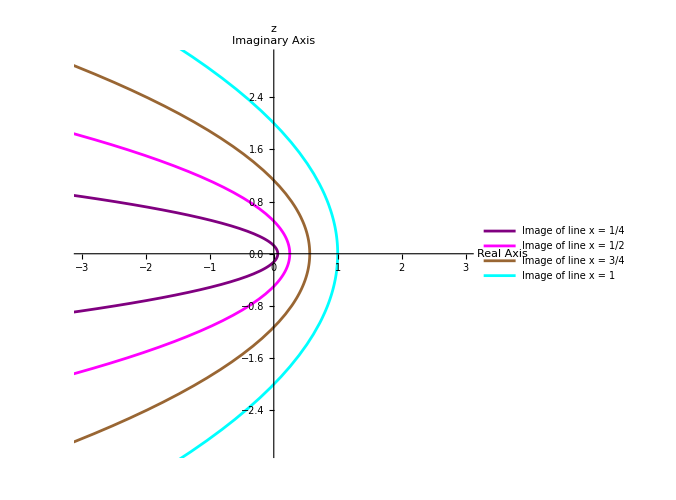

```mathematica
b2 = ParametricPlot[ Evaluate[Table[{Re[f[a + ⅈ t]], Im[f[a + ⅈ t]]}, {a, {1/4,1/2,3/4,1}}]], {t, -2, 2}, PlotStyle -> {Purple, Magenta, Brown, Cyan}, Axes -> True, Frame -> False, AxesLabel -> {"Real Axis", "Imaginary Axis"}, PlotLabel -> "z", PlotLegends -> {"Image of line x = 1/4 ", "Image of line x = 1/2", "Image of line x = 3/4 ", "Image of line x = 1"}, PlotRange -> 3, ImageSize -> {500, 500}]
```

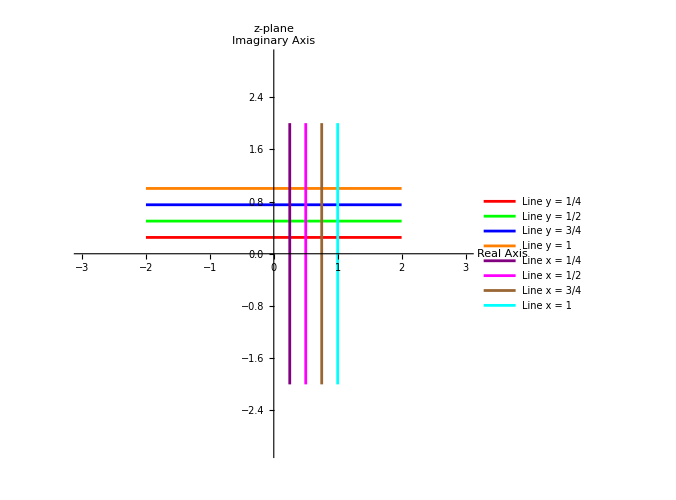
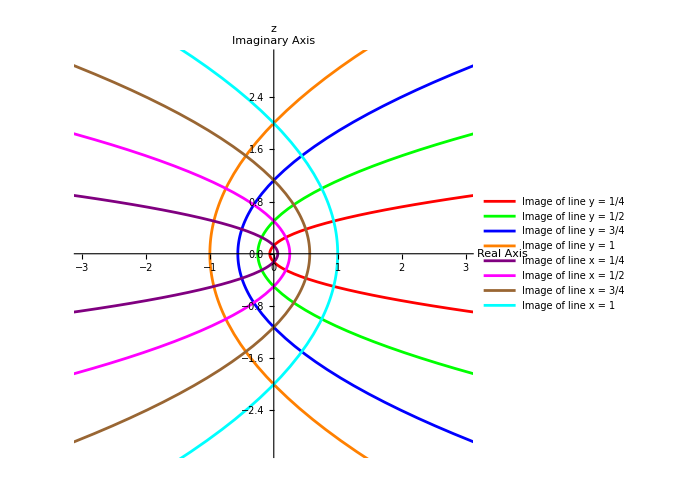

```mathematica
{Show[a1, a2], Show[b1, b2]}
```